# TetraOrigin: Haplotype reconstruction in outcrossing tetraploids

## Chaozhi Zheng Biometris, Wageningen University and Research centre 15 Feb, 2016

## Helps on “TetraOrigin`”

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]<>"\\TetraOrigin_Packages"];
(*SetDirectory["D:\\Chaozhi\\Mathematica Packages"]*)
Needs["TetraOrigin`"]
SetDirectory[NotebookDirectory[]];
?"TetraOrigin`*"
```

```mathematica
Options[inferTetraPhase]
```

{maxStuck→10,maxIteration→100,minRepeatRun→3,maxPhasingRun→20,bivalentPhasing→True}

```mathematica
?bivalentPhasing
?inferTetraPhase
```

bivalentPhasing is an option for phasing algorithm. If bivalentPhasing = True, phasing algorithm accounts for only bivalent chromosome pairing but not qudrivalent pairing. If bivalentPhasing = False, phasing algorithm accounts for both bivalent chromosome pairing and qudrivalent pairing.

inferTetraPhase[SNPDose, chrsubset, snpsubset, eps, epsF,ploidy] returns {founderhaplo, loglhistory} where founderhaplo is the estimated parental haplotypes and loglhistory is the records of log likelihood for each proposed parental haplotypes. The ploidy = 4 for tetraploid species. epsF and eps are the dosage error probabilities for parents and siblings, respectively. SNPDose is the input marker data include the genetic map and the dosages for two parents and their full sibs. chrsubset is a list of indices for linkage groups, e.g. chrsubset={1,3} the first and the third linkage groups will be analyzed, and chrsubset = "All" all the likage groups will be analyzed. snpsubset is a list of indices for SNP markers of each linkage group, e.g. snpsubset ={2, 5, 10} the second, the fifth, and the tenth markers of each linkage groups will be analyzed, and snpsubset = "All" all the markers will be analyzed.

## Example data

Simulated example data consisting: (50 full sibs + 2 parents ) x 75 SNP markers, with true dososage error eps =0. Genetic map is required with SNP locations in cM.

```mathematica
SNPDose=Import["TetraOrigin_Input_SNPDose_ExampleData.csv"];
Dimensions[SNPDose]
SNPDose[[;;10, ;;;;Round[Last[Dimensions[Rest[SNPDose]]]/9]]]//TableForm
```

{55,76}

marker | A0113 | A0241 | A0369 | A0497 | A0625 | A0753 | A0881 | A1009 | A1137
chromosome | A | A | A | A | A | A | A | A | A
position | 11.9003 | 23.5561 | 37.4988 | 48.2708 | 59.6022 | 74.8123 | 87.332 | 100.733 | 113.618
P1 | 3 | 0 | 1 | 0 | 2 | 2 | 2 | 3 | 2
P2 | 1 | 1 | 1 | 2 | 0 | 2 | 3 | 1 | 4
F1_001 | 2 | 0 | 1 | 1 | 0 | 1 | 3 | 2 | 3
F1_009 | 2 | 1 | 0 | 1 | 0 | 2 | 2 | 1 | 3
F1_017 | 3 | 1 | 1 | 1 | 0 | 3 | 2 | 2 | 4
F1_025 | 3 | 1 | 1 | 1 | 1 | 1 | 4 | 2 | 2
F1_033 | 2 | 0 | 2 | 0 | 1 | 2 | 2 | 1 | 3

Input CSV formatted data

Rows 1-3 show the genetic map.

The rest shows SNP dosage data for two parents and sampled full sibs.

Dosage ranges from 0 to 4 for a tetraploid species.

## Haplotype phasing

Estimating parental likage phases, assume only bivalent chromosome pairing.

```mathematica
{chrsubset,snpsubset}={"All","All"};  epsF=0;eps=10^(-3.); ploidy=4;{esthaplo,loglhistory}=inferTetraPhase[SNPDose,chrsubset,snpsubset,eps,epsF,ploidy,bivalentPhasing->True];
```

Start Date =Mon 15 Feb 2016 11:41:54. Chromosome  = A

Finish Phasing Date =Mon 15 Feb 2016 11:42:49. Time used in Phasing = 55.5 Seconds. log posterior of phasing runs = {-1813.36,-1813.36,-2195.49,-1813.36}

```mathematica
{esthaplo[[All,;;;;10]]//TableForm,loglhistory//TableForm}
```

{SNP | A0145 | A0305 | A0465 | A0625 | A0785 | A0945 | A1105
Chromosome | A | A | A | A | A | A | A
P1_1 | 1 | 1 | 2 | 2 | 1 | 2 | 1
P1_2 | 2 | 1 | 1 | 1 | 2 | 1 | 2
P1_3 | 1 | 1 | 1 | 2 | 1 | 1 | 1
P1_4 | 1 | 1 | 2 | 1 | 2 | 2 | 2
P2_1 | 1 | 2 | 1 | 1 | 1 | 1 | 2
P2_2 | 2 | 1 | 1 | 1 | 1 | 2 | 1
P2_3 | 2 | 2 | 2 | 1 | 1 | 1 | 2
P2_4 | 2 | 1 | 1 | 1 | 2 | 1 | 1,-7704.95
-2470.31
-1813.36
-1813.36 | -7298.65
-3063.44
-1813.36
-1813.36 | -7421.22
-2989.09
-2442.65
-2195.49
-2196.02
-2196.02
-2196.02
-2196.02
-2196.02
-2196.02
-2249.03
-2196.02
-2379.99
-2196.02 | -7265.96
-3955.48
-3115.55
-1813.36
-1813.36}

## Haplotype phasing (cont.)

The estimated haplotypes vs the true haplotypes

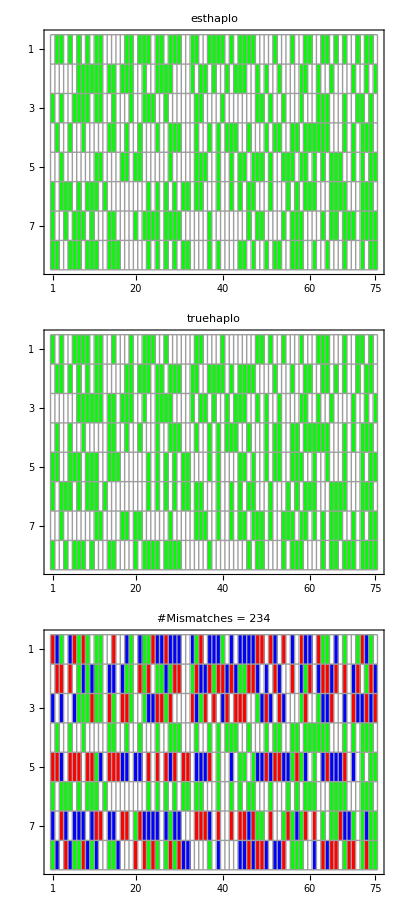

```mathematica
(*refhaplo refers to the true parental haplotypes.*)
refhaplo=Import["TetraOrigin_Truevalues_founderhaplo_ExampleData.csv"];
gg1=MatrixPlot[esthaplo[[3;;,2;;]]-1,ColorRules->{0->White,1->Green},Mesh->All,ImageSize->650,PlotLabel->"esthaplo"];
gg2=MatrixPlot[refhaplo[[3;;,2;;]]-1,ColorRules->{0->White,1->Green},Mesh->All,ImageSize->650,PlotLabel->"truehaplo"];
haplo=esthaplo;
diffhaplo=Replace[MapThread[List,{haplo[[3;;,2;;]],refhaplo[[3;;,2;;]]},2],{{1,1}->0,{1,2}->1,{2,1}->2,{2,2}->3},{2}];
dis=Total[Flatten[Abs[haplo[[3;;,2;;]]-refhaplo[[3;;,2;;]]]]];
gg3=MatrixPlot[diffhaplo,ColorRules->{0->White,1->Red,2->Blue,3->Green},Frame->True,ImageSize->650,ColorFunctionScaling->False,MaxPlotPoints->Infinity,Mesh->All,PlotLabel->"#Mismatches = "<>ToString[dis]];
Column[{gg1,gg2,gg3}]
```

Relabel the estimated haplotypes withe respect to the true haplotypes.

```mathematica
founderhaplo=relabelHaplo[esthaplo,refhaplo];
founderhaplo[[3;;,2;;]]==refhaplo[[3;;,2;;]]
```

True

## Estimating dosage error probability

Calculate the log likelihood given estimated parental hapotypes.

```mathematica
{chrsubset,snpsubset}={"All","All"}; eps=10^(-3.); ploidy=4;
loglTetraOrigin[SNPDose, chrsubset, snpsubset,eps, esthaplo,ploidy,bivalentDecoding->True] //AbsoluteTiming
loglTetraOrigin[SNPDose, chrsubset, snpsubset,eps, esthaplo,ploidy,bivalentDecoding->False] //AbsoluteTiming
```

{0.87361,-1813.36}

{11.94975,-1186.16}

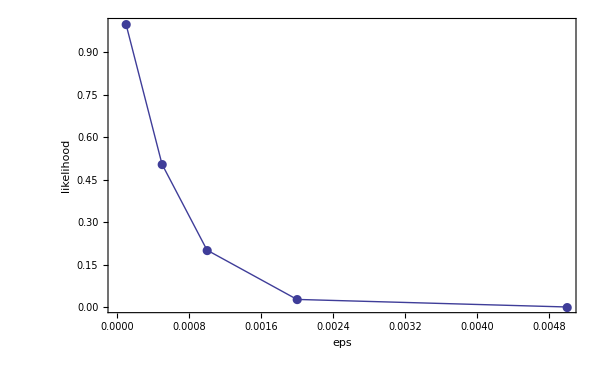

```mathematica
ls=Table[logl=loglTetraOrigin[SNPDose, chrsubset, snpsubset, x, esthaplo,ploidy,bivalentDecoding->False] ;
PrintTemporary["{eps,logl} = "<>ToString[{x,logl}]];{x,logl},{x,{0.0001,0.0005,0.001,0.002,0.005}}];
ls[[All,2]]=Exp[ls[[All,2]]-Max[ls[[All,2]]]];
ListPlot[ls,Frame->{{True,False},{True,False}},FrameLabel->{"eps","likelihood"},ImageSize->600,PlotMarkers->{Automatic,12},Joined->True,LabelStyle->Directive[FontFamily->"Helvetica",FontSize->20]]
```

## Posterior decoding

```mathematica
Options[inferTetraOrigin]
```

{maxStuck→10,maxIteration→100,minRepeatRun→3,maxPhasingRun→20,bivalentPhasing→True,bivalentDecoding→False}

```mathematica
?inferTetraOrigin
```

inferTetraOrigin[SNPDose, chrsubset, snpsubset, eps, founderhaplo, ploidy, outputid] calculates the posterior probabilities for each sib at each SNP marker given the the parental haplotype founderhaplo, and the results are saved in the file "TetraOrigin_Output_outputid_LinkageGroupA.txt" for the linkage group A, and so on for the rest linkage groups. Refer to inferTetraPhase for estimating parental haplotype and descriptions of other paremters. 
inferTetraOrigin[SNPDose, chrsubset, snpsubset, eps, epsF, ploidy, outputid] is a combination of {founderhaplo, loglhistory}= inferTetraPhase[SNPDose, chrsubset, snpsubset, eps, epsF,ploidy] and inferTetraOrigin[SNPDose, chrsubset, snpsubset, eps, epsF,ploidy, founderhaplo, outputid].

```mathematica
outputid="ExampleData";
inferTetraOrigin[SNPDose,chrsubset,snpsubset,eps,founderhaplo,ploidy,outputid,bivalentPhasing->True,bivalentDecoding->False];
```

Start Date =Mon 15 Feb 2016 11:44:04. Outputfile=TetraOrigin_Output_ExampleData_LinkageGroupA.txt

Finish Date =Mon 15 Feb 2016 11:44:26. Time used in Posteriordecoding = 21.8 Seconds.

--------------------------------------------------------------------------------------

## Summary the TetraOrigin output

Re-save the output of inferTetraOrigin as summary.

```mathematica
tetraResultFile="TetraOrigin_Output_"<>outputid<>"_LinkageGroupA.txt"
summaryFile=StringReplace[tetraResultFile,{".txt"->"_Summary.csv"}]
saveAsSummaryITO[tetraResultFile,summaryFile];
```

TetraOrigin_Output_ExampleData_LinkageGroupA.txt

TetraOrigin_Output_ExampleData_LinkageGroupA_Summary.csv

Import the summary for further analysis in mathematica

```mathematica
res=getSummaryITO[summaryFile]; 
First[res]//MatrixForm
```

(inferTetraOrigin-Summary | Genetic map of biallelic markers
inferTetraOrigin-Summary | MAP of parental haplotypes
inferTetraOrigin-Summary | Reference haplotypes
inferTetraOrigin-Summary | ln marginal likelihood of each valent of each sib
inferTetraOrigin-Summary | ln marginal likelihood given the LG type of each sib
inferTetraOrigin-Summary | Genotypes in order
inferTetraOrigin-Summary | Conditonal genotype probability
inferTetraOrigin-Summary | Conditonal haplotype probability)

## Conidtional posterior probability

Posterior haplotype porbabilities at markers of each sampled lines.

```mathematica
haploprob=res[[-1]];
trueorig=Partition[Import["TetraOrigin_Truevalues_siborig_ExampleData.csv"][[3;;,2;;]],4];
gg=Table[
lineorig=Transpose[trueorig[[line]]];
Show[MatrixPlot[Reverse[Transpose[haploprob[[line]]]],ColorFunctionScaling->True,ImageSize->1000,MaxPlotPoints->Infinity,DataRange->{{1,Dimensions[haploprob][[2]]},{1,Dimensions[haploprob][[3]]}},PlotLabel->ToString[line]<>"th Line "<>". RedLevel=Posterior Probability, Black X =True Haplotype.",FrameLabel->{"Origin","SNP"},LabelStyle->Directive[FontFamily->"Helvetica",FontSize->15]],
ListPlot[Flatten[MapIndexed[Thread[{First[#2],#1}]&,lineorig],1],PlotRange->{{1,Dimensions[haploprob][[2]]},{1,Dimensions[haploprob][[3]]}},PlotRangePadding->0,PlotMarkers->{"×",10},PlotStyle->Black]],{line,Length[haploprob]}];
ListAnimate[gg,DefaultDuration->Length[gg]]
```

## Put together

{esthaplo,loglhistory}=inferTetraPhase[SNPDose,chrsubset,snpsubset,eps,epsF,ploidy,bivalentPhasing→True];
founderhaplo=relabelHaplo[esthaplo,refhaplo];
inferTetraOrigin[SNPDose,chrsubset,snpsubset,eps,founderhaplo,ploidy,outputid,bivalentPhasing→True,bivalentDecoding→False];
(*Analyze results of Linkage groups one by one*)
tetraResultFile="TetraOrigin_Output_"<>outputid<>"_LinkageGroupA.txt";
summaryFile=StringReplace[tetraResultFile,{".txt"→"_Summary.csv"}];
saveAsSummaryITO[tetraResultFile,summaryFile];

Altenatively

inferTetraOrigin[SNPDose,chrsubset,snpsubset,eps,epsF,ploidy,outputid,bivalentPhasing→True,bivalentDecoding→False];
tetraResultFile="TetraOrigin_Output_"<>outputid<>"_LinkageGroupA.txt";
summaryFile=StringReplace[tetraResultFile,{".txt"→"_Summary.csv"}];
refhaploFile="TetraOrigin_Truevalues_founderhaplo_ExampleData.csv";
saveAsSummaryITO[tetraResultFile,summaryFile,refhaploFile];

## Referece

Chaozhi Zheng, Roeland E. Voorrips, Johannes Jansen, Christine A. Hackett, Julie Ho, and Marco C.A.M. Bink. 2016. Probabilistic multilocus haplotype reconstruction in outcrossing tetraploids.